# Setup

```mathematica
Get["FunKit`"]
```

Welcome to  █▀ ▐▄█ █▚▌ ▐◀ █ ▀█▀
Author: Franz Richard Sattler
Version: 0.2.1
Year: 2025
For more information and a brief introduction to the package, call FInfo[].
To run the testing suite, you can call  FTest[].

```mathematica
TBConstructVertexBasis[
"Name"->"σσ",
"RequiredGroups"->{{flavor,SUNfund,Nf}},
"Vertex"->{σ,σ},
"VertexStructure"->Tensor[1,2],
"CanonicalProduct"->Tensor1[1,2]Tensor2[1,2],
"Indices"->{{p1},{p2}},
"Tensors"->{{1}}]
TBConstructVertexBasis[
"Name"->"ΠΠ",
"RequiredGroups"->{{flavor,SUNfund,Nf}},
"Vertex"->{Π,Π},
"VertexStructure"->Tensor[1,2],
"CanonicalProduct"->Tensor1[1,2]Tensor2[1,2],
"Indices"->{{p1,f1},{p2,f2}},
"Tensors"->{{deltaAdjFlav[f1,f2]}}]
TBConstructVertexBasis[
"Name"->"ΠΠσ",
"RequiredGroups"->{{flavor,SUNfund,Nf}},
"Vertex"->{Π,Π,σ},
"VertexStructure"->Tensor[1,2,3],
"CanonicalProduct"->Tensor1[1,2,3]Tensor2[1,2,3],
"Indices"->{{p1,f1},{p2,f2},{p3}},
"Tensors"->{{deltaAdjFlav[f1,f2]}}]
TBConstructVertexBasis[
"Name"->"ΠΠσσ",
"RequiredGroups"->{{flavor,SUNfund,Nf}},
"Vertex"->{Π,Π,σ,σ},
"VertexStructure"->Tensor[1,2,3,4],
"CanonicalProduct"->Tensor1[1,2,3,4]Tensor2[1,2,3,4],
"Indices"->{{p1,f1},{p2,f2},{p3},{p4}},
"Tensors"->{{deltaAdjFlav[f1,f2]}}]
TBConstructVertexBasis[
"Name"->"σσσ",
"RequiredGroups"->{{flavor,SUNfund,Nf}},
"Vertex"->{σ,σ,σ},
"VertexStructure"->Tensor[1,2,3],
"CanonicalProduct"->Tensor1[1,2,3]Tensor2[1,2,3],
"Indices"->{{p1},{p2},{p3}},
"Tensors"->{{1}}]
TBConstructVertexBasis[
"Name"->"σσσσ",
"RequiredGroups"->{{flavor,SUNfund,Nf}},
"Vertex"->{σ,σ,σ,σ},
"VertexStructure"->Tensor[1,2,3,4],
"CanonicalProduct"->Tensor1[1,2,3,4]Tensor2[1,2,3,4],
"Indices"->{{p1},{p2},{p3},{p4}},
"Tensors"->{{1}}]
TBConstructVertexBasis[
"Name"->"ΠΠΠΠ",
"RequiredGroups"->{{flavor,SUNfund,Nf}},
"Vertex"->{Π,Π,Π,Π},
"VertexStructure"->Tensor[1,2,3,4],
"CanonicalProduct"->Tensor1[1,2,3,4]Tensor2[1,2,3,4],
"Indices"->{{p1,f1},{p2,f2},{p3,f3},{p4,f4}},
"Tensors"->{{deltaAdjFlav[f1,f2]deltaAdjFlav[f3,f4]}}]
```

```mathematica
fields= <|"Commuting"-> {Π[p,{f}],σ[p]}|>;

truncation=<|
GammaN->{
{σ},
{Π,Π},{σ,σ},
{Π,Π,σ},{σ,σ,σ},
{Π,Π,Π,Π},{Π,Π,σ,σ},{σ,σ,σ,σ}
},
Propagator->{{Π,Π},{σ,σ}},
Rdot->{{Π,Π},{σ,σ}},
Field->{{σ}},
Phidot->{
{σ},{σ,σ},{σ,σ,σ},
{Π,Π,σ},
{Π,Π},{σ,Π,Π}
},
R->{{Π,Π},{σ,σ}}
|>;

bases=<|
GammaN->{
{Π,Π}->"ΠΠ",{σ,σ}->"σσ",
{Π,Π,Π,Π}->"ΠΠΠΠ",
{Π,Π,σ,σ}->"ΠΠσσ",
{Π,Π,σ}->"ΠΠσ",
{σ,σ,σ}->"σσσ",
{σ,σ,σ,σ}->"σσσσ"
},
Propagator->{{Π,Π}->"ΠΠ",{σ,σ}->"σσ"},
R->{{Π,Π}->"ΠΠ",{σ,σ}->"σσ"},
Rdot->{{Π,Π}->"ΠΠ",{σ,σ}->"σσ"}
|>;

diagramStyling=<|
"Styles"->{Π->{Black},σ->{Black,Dashed}},
"Vertices"->{Phidot}
|>;
```

```mathematica
Setup=<|
"FieldSpace"->fields,
"Truncation"->truncation,
"DiagramStyling"->diagramStyling,
"FeynmanRules"->bases
|>;
FSetGlobalSetup[Setup];
```

```mathematica
PhidotRules={
Phidot[{Π,Π},{{p1_,{f1_}},{p_,{f_}}}]:>deltaAdjFlav[f,f1]ZPi[p1],
Phidot[{σ,Π,Π},{{p2_},{p1_,{f1_}},{p_,{f_}}}]:>deltaAdjFlav[f,f1]dZPi[p1],
Phidot[{σ},{{p_}}]:>sigma ZSig[p],
Phidot[{σ,σ},{{p1_},{p_}}]:>sigma^2 dZSig[p]+ ZSig[p1],
Phidot[{σ,σ,σ},{{p2_},{p1_},{p_}}]:>3sigma dZSig[p]+ sigma^2 ddZSig[p1],
Phidot[{Π,Π,σ},{{p2_,{f2_}},{p1_,{f1_}},{p_}}]:>deltaAdjFlav[f1,f2]dZSigma[p1],
GammaN[{σ},{{p_}}]:>sigma
};
```

# Flows

```mathematica
GeneralizedFlowEquationRHS=GeneralizedFlowEquation[[2;;]]//FPrint;
GeneralizedFlowEquationLHS=GeneralizedFlowEquation[[1]]//FPrint;
```

-Graphics-

-Graphics-

## Pion propagator


-Graphics-+-Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-

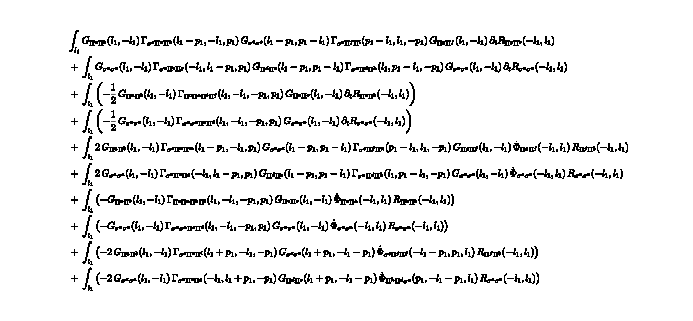

{((-1+Nf^2) dressing[GammaN,{σ,Π,Π},1,{l1-p1,-l1,p1}] dressing[GammaN,{σ,Π,Π},1,{-l1+p1,l1,-p1}] dressing[Rdot,{Π,Π},1,{-l1,l1}])/(dressing[InverseProp,{Π,Π},1,{l1,-l1}]^2 dressing[InverseProp,{σ,σ},1,{l1-p1,-l1+p1}]),((-1+Nf^2) dressing[GammaN,{σ,Π,Π},1,{-l1,l1-p1,p1}] dressing[GammaN,{σ,Π,Π},1,{l1,-l1+p1,-p1}] dressing[Rdot,{σ,σ},1,{-l1,l1}])/(dressing[InverseProp,{Π,Π},1,{l1-p1,-l1+p1}] dressing[InverseProp,{σ,σ},1,{l1,-l1}]^2),-((-1+Nf^2)^2 dressing[GammaN,{Π,Π,Π,Π},1,{l1,-l1,-p1,p1}] dressing[Rdot,{Π,Π},1,{-l1,l1}])/(2 dressing[InverseProp,{Π,Π},1,{l1,-l1}]^2),-((-1+Nf^2) dressing[GammaN,{σ,σ,Π,Π},1,{l1,-l1,-p1,p1}] dressing[Rdot,{σ,σ},1,{-l1,l1}])/(2 dressing[InverseProp,{σ,σ},1,{l1,-l1}]^2),(2 (-1+Nf^2) dressing[GammaN,{σ,Π,Π},1,{l1-p1,-l1,p1}] dressing[GammaN,{σ,Π,Π},1,{-l1+p1,l1,-p1}] dressing[R,{Π,Π},1,{-l1,l1}] ZPi[-l1])/(dressing[InverseProp,{Π,Π},1,{l1,-l1}]^2 dressing[InverseProp,{σ,σ},1,{l1-p1,-l1+p1}]),(2 (-1+Nf^2) dressing[GammaN,{σ,Π,Π},1,{-l1,l1-p1,p1}] dressing[GammaN,{σ,Π,Π},1,{l1,-l1+p1,-p1}] dressing[R,{σ,σ},1,{-l1,l1}] (sigma^2 dZSig[l1]+ZSig[-l1]))/(dressing[InverseProp,{Π,Π},1,{l1-p1,-l1+p1}] dressing[InverseProp,{σ,σ},1,{l1,-l1}]^2),-((-1+Nf^2)^2 dressing[GammaN,{Π,Π,Π,Π},1,{l1,-l1,-p1,p1}] dressing[R,{Π,Π},1,{-l1,l1}] ZPi[-l1])/dressing[InverseProp,{Π,Π},1,{l1,-l1}]^2,-((-1+Nf^2) dressing[GammaN,{σ,σ,Π,Π},1,{l1,-l1,-p1,p1}] dressing[R,{σ,σ},1,{-l1,l1}] (sigma^2 dZSig[l1]+ZSig[-l1]))/dressing[InverseProp,{σ,σ},1,{l1,-l1}]^2,-(2 (-1+Nf^2) dressing[GammaN,{σ,Π,Π},1,{l1+p1,-l1,-p1}] dressing[R,{Π,Π},1,{-l1,l1}] dZPi[p1])/(dressing[InverseProp,{Π,Π},1,{l1,-l1}] dressing[InverseProp,{σ,σ},1,{l1+p1,-l1-p1}]),-(2 (-1+Nf^2) dressing[GammaN,{σ,Π,Π},1,{-l1,l1+p1,-p1}] dressing[R,{σ,σ},1,{-l1,l1}] dZSigma[-l1-p1])/(dressing[InverseProp,{Π,Π},1,{l1+p1,-l1-p1}] dressing[InverseProp,{σ,σ},1,{l1,-l1}])}

```mathematica
fRGΠΠ=FTakeDerivatives[GeneralizedFlowEquationRHS,{Π[i1],Π[i2]}]//FTruncate//FPlot//FRoute//FPrint;
projΠΠ=FTerm[deltaAdjFlav[f1,f2]];
flowΠΠRHS=FormTrace[projΠΠ**fRGΠΠ["1-Loop"]["Expression"]/.FMakeDiagrammaticRules[]/.PhidotRules]
```

## Sigma propagator

-Graphics-+-Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-

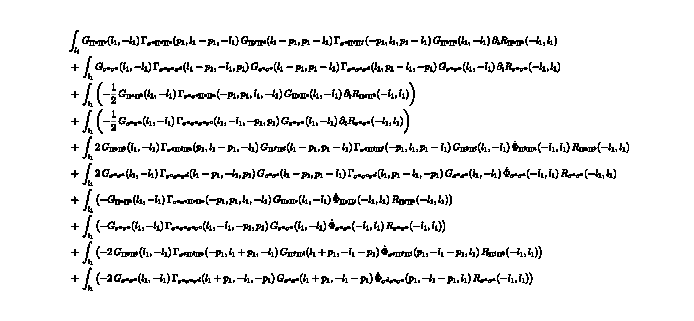

```mathematica
fRGσσRHS=FTakeDerivatives[GeneralizedFlowEquationRHS,{σ[i1],σ[i2]}]//FTruncate//FPlot//FRoute//FPrint;
```

```mathematica
flowσσRHS=FormTrace[fRGσσRHS["1-Loop"]["Expression"]/.FMakeDiagrammaticRules[]/.PhidotRules]//Total//Simplify
```

-(2 sigma^2 ddZSig[-l1-p1] dressing[GammaN,{σ,σ,σ},1,{l1+p1,-l1,-p1}] dressing[R,{σ,σ},1,{-l1,l1}])/(dressing[InverseProp,{σ,σ},1,{l1,-l1}] dressing[InverseProp,{σ,σ},1,{l1+p1,-l1-p1}])+1/(2 dressing[InverseProp,{Π,Π},1,{l1,-l1}]^2)(-((-1+Nf^2) dressing[GammaN,{σ,σ,Π,Π},1,{-p1,p1,l1,-l1}] (dressing[Rdot,{Π,Π},1,{-l1,l1}]+2 dressing[R,{Π,Π},1,{-l1,l1}] ZPi[-l1]))+(2 (-1+Nf^2) dressing[GammaN,{σ,Π,Π},1,{-p1,l1,-l1+p1}] dressing[GammaN,{σ,Π,Π},1,{p1,l1-p1,-l1}] (dressing[Rdot,{Π,Π},1,{-l1,l1}]+2 dressing[R,{Π,Π},1,{-l1,l1}] ZPi[-l1]))/dressing[InverseProp,{Π,Π},1,{l1-p1,-l1+p1}]+(2 dressing[GammaN,{σ,σ,σ},1,{l1,-l1+p1,-p1}] dressing[GammaN,{σ,σ,σ},1,{l1-p1,-l1,p1}] dressing[InverseProp,{Π,Π},1,{l1,-l1}]^2 (dressing[Rdot,{σ,σ},1,{-l1,l1}]+2 dressing[R,{σ,σ},1,{-l1,l1}] (sigma^2 dZSig[l1]+ZSig[-l1])))/(dressing[InverseProp,{σ,σ},1,{l1,-l1}]^2 dressing[InverseProp,{σ,σ},1,{l1-p1,-l1+p1}])+1/dressing[InverseProp,{σ,σ},1,{l1,-l1}]^2 dressing[InverseProp,{Π,Π},1,{l1,-l1}] (4 dressing[InverseProp,{σ,σ},1,{l1,-l1}] (-(((-1+Nf^2) dressing[GammaN,{σ,Π,Π},1,{-p1,l1+p1,-l1}] dressing[InverseProp,{σ,σ},1,{l1,-l1}] dressing[R,{Π,Π},1,{-l1,l1}] dZPi[-l1-p1])/dressing[InverseProp,{Π,Π},1,{l1+p1,-l1-p1}])-(3 sigma dressing[GammaN,{σ,σ,σ},1,{l1+p1,-l1,-p1}] dressing[InverseProp,{Π,Π},1,{l1,-l1}] dressing[R,{σ,σ},1,{-l1,l1}] dZSig[l1])/dressing[InverseProp,{σ,σ},1,{l1+p1,-l1-p1}])-dressing[GammaN,{σ,σ,σ,σ},1,{l1,-l1,-p1,p1}] dressing[InverseProp,{Π,Π},1,{l1,-l1}] (dressing[Rdot,{σ,σ},1,{-l1,l1}]+2 dressing[R,{σ,σ},1,{-l1,l1}] (sigma^2 dZSig[l1]+ZSig[-l1]))))


-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-

-Graphics-

```mathematica
fRGσσLHS=FTakeDerivatives[GeneralizedFlowEquationLHS,{σ[i1],σ[i2]}]//FTruncate//FPlot//FRoute//FPrint;
```

```mathematica
flowσσLHS=FormTrace[fRGσσLHS["0-Loop"]["Expression"]/.FMakeDiagrammaticRules[]/.PhidotRules]//Total//Simplify
```

-sigma^3 ddZSig[p1]-sigma (3 sigma dZSig[0]+dressing[GammaN,{σ,σ,σ},1,{-p1,p1,0}] ZSig[0])-2 dressing[GammaN,{σ,σ},1,{p1,-p1}] (sigma^2 dZSig[p1]+ZSig[-p1])

## Meson Potential

-Graphics-+-Graphics-+-Graphics--Graphics-+-Graphics--Graphics-

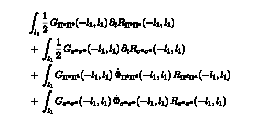

```mathematica
fRGVRHS=GeneralizedFlowEquationRHS//FTruncate//FSimplify//FPlot//FRoute//FPrint;
```

```mathematica
flowVRHS=FormTrace[fRGVRHS["1-Loop"]["Expression"]/.FMakeDiagrammaticRules[]/.PhidotRules]//Total//Simplify
```

1/2 (((-1+Nf^2) (dressing[Rdot,{Π,Π},1,{-l1,l1}]+2 dressing[R,{Π,Π},1,{-l1,l1}] ZPi[-l1]))/dressing[InverseProp,{Π,Π},1,{-l1,l1}]+(dressing[Rdot,{σ,σ},1,{-l1,l1}]+2 dressing[R,{σ,σ},1,{-l1,l1}] (sigma^2 dZSig[l1]+ZSig[-l1]))/dressing[InverseProp,{σ,σ},1,{-l1,l1}])

```mathematica
fRGVLHS=GeneralizedFlowEquationLHS//FEx//FTruncate//FPlot//FRoute//FPrint;
flowVLHS=FormTrace[fRGVLHS["1-Loop"]["Expression"]/.FMakeDiagrammaticRules[]/.PhidotRules]//Total//Simplify
```

-Graphics--Graphics-

-Graphics-

-sigma^2 ZSig[l1]